# Splitsing energie niveau’s

## Rechthoek LCA

De invloed van L/Wop de energie niveaus wordt hier onderzocht. Dit komt overeen met het uitrekken langs x voor L>W of uitrekken langs y als L<W. Bij het uitrekken houden we het oppervlak van de figuur constant. Het oplossen van de vergelijkingen LW=1 en L/W=x geeft een uitdrukking voor W en L in functie van x die zal varieren van 0.8 tot 1.2.

```mathematica
Clear["Global`*"]
n = 13;
Ω = 1/Sqrt[2 Pi];
eigval[lijst_] := ((lijst[[1]] Pi)/L)^2+((lijst[[2]]  Pi)/W)^2
λlist := Part[SortBy[Tuples[Range[0,n],2], eigval[#]&],1;;n];
eigvals := Table[((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2, {i, 1, n}];
```

```mathematica
list = {};
For[x=0.01,x≤ 2, x+=0.01, {L=Sqrt[x];W=1/Sqrt[x];AppendTo[list, eigvals]}]
```

```mathematica
r = Table[(((i)*0.01)),{i,1,200}];
data = Table[Transpose@{r, Sqrt[list[[;;,i]]]},{i,1,n}];
```

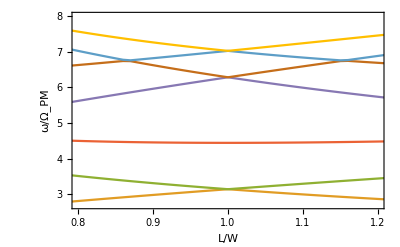

```mathematica
ListPlot[data, PlotRange->{{0.8,1.2},{2.7,8}},Joined->True, Frame->True,FrameLabel->{{Style["ω/Ω_PM",Bold,16],""},{Style["L/W",Bold,16],""}}]
```

## Driehoek LCA

Er wordt een gelijkbenige driehoek beschouwd met basis b en hoogte h. Opnieuw wordt de oppervlakte constant gehouden bij de transformaties op 1. De hoogste symmetrie is er bij b/h = 2/(√3) want dan is de driehoek gelijkzijdig.

```mathematica
Clear["Global`*"]
n = 8;
list = {};
For[r=0.01,r≤ 2, r+=0.01, {b=Sqrt[2 r];h=Sqrt[2/r]; t=Triangle[{{0,0},{b,0},{b/2,h}}];{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y}∈ t]}, u, {x,y} ∈ t, n];AppendTo[list, vals]}]
```

Eigensystem::ssing: Failed to factor the matrix involving the shift. This may be caused by the shift, {3.37221×10^-11}, corresponding exactly to an eigenvalue. Changing the shift value slightly might help.

Set::shape: Lists {vals,funs} and NDEigensystem[{NeumannValue[0,{x,y}∈Triangle[{{«2»},{«2»},{«2»}}]]-u^(0,2)[x,y]-u^(2,0)[x,y]},u,{x,y}∈Triangle[{{0,0},{1.24097,0},{0.620484,1.61165}}],8] are not the same shape.

Eigensystem::ssing: Failed to factor the matrix involving the shift. This may be caused by the shift, {3.37221×10^-11}, corresponding exactly to an eigenvalue. Changing the shift value slightly might help.

```mathematica
r = Table[(((i)*0.01)),{i,1,200}];
data = Table[Transpose@{r, Sqrt[Abs[list[[;;,i]]]]},{i,1,n}];
```

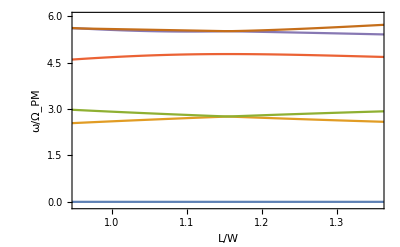

```mathematica
ListPlot[data, PlotRange->{{2/Sqrt[3]-0.20,2/Sqrt[3]+0.20},{-0.1,6}},Joined->True, Frame->True,FrameLabel->{{Style["ω/Ω_PM",Bold,16],""},{Style["L/W",Bold,16],""}}]
```

## Schijf LCA

```mathematica
Clear["Global`*"]
n = 8;
list = {};
For[r=0.6,r≤1.4,r+=0.01,{R={Sqrt[r/Pi], Sqrt[1/(r Pi)]}; {vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y} ∈ Circle[{0,0}, R]]}, u, {x,y} ∈ Disk[{0,0}, R], n]; AppendTo[list, vals]}]
r = Table[0.59+i*0.01,{i,1,81}];
data = Table[Transpose@{r,Sqrt[Abs[list]][[;;,i]]}, {i,1,n}];
```

Eigensystem::ssing: Failed to factor the matrix involving the shift. This may be caused by the shift, {3.37221×10^-11}, corresponding exactly to an eigenvalue. Changing the shift value slightly might help.

Set::shape: Lists {vals,funs} and NDEigensystem[{NeumannValue[0,{x,y}∈Circle[{0,0},{0.635809,0.500637}]]-u^(0,2)[x,y]-u^(2,0)[x,y]},u,{x,y}∈Disk[{0,0},{0.635809,0.500637}],8] are not the same shape.

Eigensystem::ssing: Failed to factor the matrix involving the shift. This may be caused by the shift, {3.37221×10^-11}, corresponding exactly to an eigenvalue. Changing the shift value slightly might help.

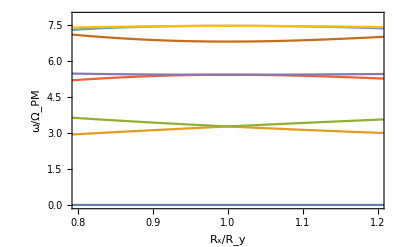

```mathematica
ListPlot[data, Joined->True, Frame->True,FrameLabel->{Style["R_x/R_y",16,Bold],Style["ω/Ω_PM",16,Bold]},PlotRange->{{0.8,1.2},All}]
```